# c.quark-flow.decompose.channal-value.EM.paper.nb

## initial

```mathematica
(*计算环境参量，比如路径*)
gitRemoteName="octet.formfactor";(*给出远程git仓库的名字*)
cmdQ=Not[$Notebooks];(*脚本的运行模式判断，True代表命令行，False代表前端*)
fileName=If[Not[cmdQ],NotebookFileName[],$InputFileName](*给出笔记本的绝对路径*)
(*定义一些常用的函数*)
enList[x__]:=Replace[{x},{{y__}}:>{y},{0}](*定义一个确保列表的函数*)
enString[x__]:=StringJoin[ToString[#1]&/@enList[x]](*定义一个确保字符串的函数*)
If[cmdQ,
echo[x__]:=Print["----------------------------","\n\033[1;44m\033[1;37m",enString[x],"\033[0;0m\n","----------------------------"],(*定义终端的打印函数*)
echo[x__]:=Print[x](*定义笔记本的打印函数*)
]
(*如果在前端执行，就刷新笔记本的名字*)
Once[If[
(* if $ScriptCommandLine==={}, the environment is frontend*)
Not[cmdQ],
(*if execute in the frontend mode, refresh the title name*)
CompoundExpression[
cellTitle=(Cells[][[1]]),(*单元对象,第一个单元*)
NotebookWrite[cellTitle,Cell[FileNameSplit[fileName][[-1]],"Title"]](*刷新第一个单元的名字*)
]
]];
If[cmdQ,echo["Ready to execute this script"]](*如果在命令行执行，就打印提示信息*)
(*定义本地git目录，也就是程序的根目录*)
echo["the gitLocalName is"]
gitLocalName=FileNameJoin[Append[TakeWhile[FileNameSplit[ExpandFileName[fileName]],UnsameQ[#1,gitRemoteName]&],gitRemoteName]]
```

这个笔记本用来展示夸克流 channel->value 的表格，方便在论文中使用。

## initial

```mathematica
(*系数存放的目录*)
coeDir=FileNameJoin[{gitLocalName,"/expression-coes/"}];
(*导入fucoeandmrrlabbr*)
fucoeandmrrlabbr1symmetry=Get[FileNameJoin[{coeDir,"fucoeandmrrlabbr.symmetry.m"}]];
fucoeandmrrlabbr1normal=Get[FileNameJoin[{coeDir,"fucoeandmrrlabbr.normal.m"}]];
(*this fucoeandmrrlabbr 的约化系数是1，不用考虑 fucancoel*)
```

## chpt eta coes

```mathematica
name1chpt1eta1symbolic1symmetry=FileNameJoin[{Directory[],"chpt1eta1symbolic1symmetry.m"}];
name1chpt1eta1symbolic1normal=FileNameJoin[{Directory[],"chpt1eta1symbolic1normal.m"}];
```

```mathematica
Once[chpt1eta1symbolic1symmetry=Get[name1chpt1eta1symbolic1symmetry]];
Once[chpt1eta1symbolic1normal=Get[name1chpt1eta1symbolic1normal]];
```

## reassign the eta values

```mathematica
chpt1eta1names1uneed=Table[
Select[
Keys[fucoeandmrrlabbr1symmetry⟦flavor,if,io⟧],(*the chpt names*)
Or[
Equal[StringExtract[ToString[#],"1"->-1],"ηl"],
Equal[StringExtract[ToString[#],"1"->-1],"ηs"]
]&(*select the ones contain ηl and ηs, maybe only ηl*)
]
,{flavor,1,3,1}
,{if,1,5,1}
,{io,1,8,1}
];
```

```mathematica
fucoeandmrrlabbr1symmetry1re=Table[
Merge[
Join[
chpt1eta1symbolic1symmetry⟦flavor,if,io⟧,
Normal[
KeyDrop[
Association[fucoeandmrrlabbr1symmetry⟦flavor,if,io⟧],
chpt1eta1names1uneed⟦flavor,if,io⟧]
]
]
,First(*means in the associations, pick up the chpt1eta1symbolic values*)
]/.fucoeandmrrlabbr1symmetry⟦flavor,if,io⟧
,{if,1,5,1}(*here, we change the index order in accordance with the follow part*)
,{io,1,8,1}
,{flavor,1,3,1}
];
```

```mathematica
fucoeandmrrlabbr1normal1re=Table[
Merge[
Join[
chpt1eta1symbolic1normal⟦flavor,if,io⟧,
Normal[
KeyDrop[
Association[fucoeandmrrlabbr1normal⟦flavor,if,io⟧],
chpt1eta1names1uneed⟦flavor,if,io⟧]
]
]
,First(*means in the associations, pick up the chpt1eta1symbolic values*)
]/.fucoeandmrrlabbr1normal⟦flavor,if,io⟧
,{if,1,5,1}(*here, we change the index order in accordance with the follow part*)
,{io,1,8,1}
,{flavor,1,3,1}
];
```

quench&sea&valence

```mathematica
name1quarkflow1qfb1quench=FileNameJoin[{Directory[],"quarkflow.qfb.quench.m"}];
name1quarkflow1qfa1sea=FileNameJoin[{Directory[],"quarkflow.qfa.sea.m"}];
name1quarkflow1qfa1valence=FileNameJoin[{Directory[],"quarkflow.qfa.valence.m"}];
```

```mathematica
Once[quarkflow1qfb1quench=Transpose[Get[
name1quarkflow1qfb1quench
],{3,1,2}]];
Once[quarkflow1qfa1sea=Transpose[Get[
name1quarkflow1qfa1sea
],{3,1,2}]];
Once[quarkflow1qfa1valence=Transpose[Get[
name1quarkflow1qfa1valence
],{3,1,2}]];
```

quench&sea&valence  channel

```mathematica
name1quarkflow1qfa1valence1channel=FileNameJoin[{Directory[],"quarkflow.qfa.valence.channel.m"}];
name1quarkflow1qfa1sea1channel=FileNameJoin[{Directory[],"quarkflow.qfa.sea.channel.m"}];
name1quarkflow1qfb1quench1channel=FileNameJoin[{Directory[],"quarkflow.qfb.quench.channel.m"}];
```

```mathematica
Once[quarkflow1qfa1valence1channel=Transpose[Get[
name1quarkflow1qfa1valence1channel],{3,1,2}]];
Once[quarkflow1qfa1sea1channel=Transpose[Get[
name1quarkflow1qfa1sea1channel],{3,1,2}]];
Once[quarkflow1qfb1quench1channel=Transpose[Get[name1quarkflow1qfb1quench1channel
],{3,1,2}]];
```

decompose

```mathematica
name1quarkflow1decompose1numerical=
FileNameJoin[{Directory[],"quarkflow.decompose.numerical.m"}];
name1quarkflow1decompose1symbolic=
FileNameJoin[{Directory[],"quarkflow.decompose.symbolic.m"}];
```

```mathematica
Once[quarkflow1decompose1numerical=Get[name1quarkflow1decompose1numerical]];
Once[quarkflow1decompose1symbolic=Get[name1quarkflow1decompose1symbolic]];
```

chpt-quark relation

quarkflow & chpt figures mutual conversion

```mathematica
name1chqftransfer1=
FileNameJoin[{Directory[],"chpt-to-quarkflow.m"}];
name1chqftransfer2=
FileNameJoin[{Directory[],"quarkflow-to-chpt.m"}];
```

```mathematica
Once[chpt1to1quarkflow=Get[name1chqftransfer1]];
Once[quarkflow1to1chpt=Get[name1chqftransfer2]];
```

fu1coe uds

name1fu1coe1perspective1consti1all=FileNameJoin[{Directory[],"fu.coe.perspective.consti.all.m"}];
name1fu1coe1perspective1consti1u=FileNameJoin[{Directory[],"fu.coe.perspective.consti.u.m"}];
name1fu1coe1perspective1consti1d=FileNameJoin[{Directory[],"fu.coe.perspective.consti.d.m"}];
name1fu1coe1perspective1consti1s=FileNameJoin[{Directory[],"fu.coe.perspective.consti.s.m"}];

Once[fu1coe1perspective1consti1all=Get[name1fu1coe1perspective1consti1all]];
Once[fu1coe1perspective1consti1u=Get[name1fu1coe1perspective1consti1u]];
Once[fu1coe1perspective1consti1d=Get[name1fu1coe1perspective1consti1d]];
Once[fu1coe1perspective1consti1s=Get[name1fu1coe1perspective1consti1s]];

fu1coe1perspective={
fu1coe1perspective1consti1u,
fu1coe1perspective1consti1d,
fu1coe1perspective1consti1s
};

## extend to 11 figures

```mathematica
quarkflow1qfb1quench//Dimensions
quarkflow1qfa1sea//Dimensions
quarkflow1qfa1valence//Dimensions
quarkflow1qfb1quench1channel//Dimensions
quarkflow1qfa1valence1channel//Dimensions
quarkflow1qfa1sea1channel//Dimensions
fucoeandmrrlabbr1normal1re//Dimensions
fucoeandmrrlabbr1symmetry1re//Dimensions
```

figure orders

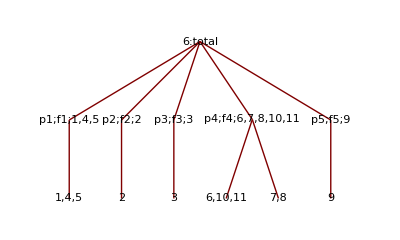

extend to 6

```mathematica
Once[fucoeandmrrlabbr1normal1re1ext6=Table[0,{if,1,6,1},{io,1,8,1},{flavor,1,3,1}]];
```

```mathematica
Once[fucoeandmrrlabbr1symmetry1re1ext6=Table[0,{if,1,6,1},{io,1,8,1},{flavor,1,3,1}]];
```

```mathematica
fucoeandmrrlabbr1normal1re1ext6⟦{1,2,3,4,5,6},;;,;;⟧=fucoeandmrrlabbr1normal1re⟦{1,2,3,4,4,5},;;,;;⟧;
```

```mathematica
fucoeandmrrlabbr1symmetry1re1ext6⟦{1,2,3,4,5,6},;;,;;⟧=fucoeandmrrlabbr1symmetry1re⟦{1,2,3,4,4,5},;;,;;⟧;
```

extend to 11 figures

this section is to extend 4 figure coes to the full 11 figures

```mathematica
Once[quarkflow1qfb1quench1extend=Table[0,{i,1,11,1}]];
Once[quarkflow1qfa1sea1extend=Table[0,{i,1,11,1}]];
Once[quarkflow1qfa1valence1extend=Table[0,{i,1,11,1}]];
```

```mathematica
Once[fucoeandmrrlabbr1extend=Table[0,{i,1,11,1}]];
```

```mathematica
Once[quarkflow1qfb1quench1channel1extend=Table[0,{i,1,11,1}]];
Once[quarkflow1qfa1valence1channel1extend=Table[0,{i,1,11,1}]];
Once[quarkflow1qfa1sea1channel1extend=Table[0,{i,1,11,1}]];
```

## fun1extendto11

```mathematica
fun1extendto11=Function[{x},
{
x⟦1⟧,(*1*)
(*////////////////////////////////*)
x⟦2⟧,(*2*)
(*////////////////////////////////*)
x⟦3⟧,(*3*)
(*////////////////////////////////*)
(*4*)ToExpression[
StringReplace[
ToString[
x⟦1⟧
,StandardForm],
"f11o"~~n:DigitCharacter:>"f41o"~~ToString[n]
]
],(*4*)
(*////////////////////////////////*)
(*5*)ToExpression[
StringReplace[
ToString[
x⟦1⟧
,StandardForm],
"f11o"~~n:DigitCharacter:>"f51o"~~ToString[n]
]
],(*5*)
(*////////////////////////////////*)
(*6*)ToExpression[
StringReplace[
ToString[
x⟦4⟧
,StandardForm],
"f41o"~~n:DigitCharacter:>"f61o"~~ToString[n]
]
],(*6*)
(*////////////////////////////////*)
(*7*)ToExpression[
StringReplace[
ToString[
x⟦5⟧
,StandardForm],
"f41o"~~n:DigitCharacter:>"f71o"~~ToString[n]
]
],(*7*)
(*////////////////////////////////*)
(*8*)ToExpression[
StringReplace[
ToString[
x⟦5⟧
,StandardForm],
"f41o"~~n:DigitCharacter:>"f81o"~~ToString[n]
]
],(*8*)
(*////////////////////////////////*)
(*9*)ToExpression[
StringReplace[
ToString[
x⟦6⟧
,StandardForm],
"f51o"~~n:DigitCharacter:>"f91o"~~ToString[n]
]
],(*9*)
(*////////////////////////////////*)
(*10*)ToExpression[
StringReplace[
ToString[
x⟦4⟧
,StandardForm],
"f41o"~~n:DigitCharacter:>"f101o"~~ToString[n]
]
],(*10*)
(*////////////////////////////////*)
(*11*)ToExpression[
StringReplace[
ToString[
x⟦4⟧
,StandardForm],
"f41o"~~n:DigitCharacter:>"f111o"~~ToString[n]
]
](*11*)
}
(*////////////////////////////////*)
];
```

## apply extend to 11

```mathematica
quarkflow1qfb1quench1extend=fun1extendto11[quarkflow1qfb1quench];
quarkflow1qfa1sea1extend=fun1extendto11[quarkflow1qfa1sea];
quarkflow1qfa1valence1extend=fun1extendto11[quarkflow1qfa1valence];
```

```mathematica
quarkflow1qfb1quench1channel1extend=fun1extendto11[quarkflow1qfb1quench1channel];
quarkflow1qfa1valence1channel1extend=fun1extendto11[quarkflow1qfa1valence1channel];
quarkflow1qfa1sea1channel1extend=fun1extendto11[quarkflow1qfa1sea1channel];
```

```mathematica
fucoeandmrrlabbr1normal1extend=fun1extendto11[fucoeandmrrlabbr1normal1re1ext6];
fucoeandmrrlabbr1symmetry1extend=fun1extendto11[fucoeandmrrlabbr1symmetry1re1ext6];
```

## 239 vertex

this part gives the chpt 2 3 9 special vertex for uds flavor

```mathematica
Once[chpt1vert1octet1electric=Table[0,{i,1,3,1}]];
Once[chpt1vert1octet1magnetic=Table[0,{i,1,3,1}]];
Once[chpt1vert1octet1transition=Table[0,{i,1,3,1}]];
```

3 position, every position corresponding to an flavor.

the vert value should corresponding to one quark, ie for u in proton(uud),should divided by 2.

chpt1vert1octet1electric

## chpt1vert1octet1electric u

```mathematica
chpt1vert1octet1electric⟦1⟧=<|
"Σm1Σm"->I el (((c1-c2+c3) Q2)/(4 mo^2+Q2)),(*Σm,Σm*)
"Σ01Σ0"->I el ((4 mo^2+(1+c1+c3) Q2)/(4 mo^2+Q2)),(*Σ0,Σ0*)
"Σp1Σp"->I el ((8 mo^2+(2+c1+c2+c3) Q2)/(2 (4 mo^2+Q2))),(*Σp,Σp*)
"Np1Np"->I el ((8 mo^2+(2+c1+c2+c3) Q2)/(2 (4 mo^2+Q2))), (*Np in, Np out, Aμ in,*)
"Nn1Nn"->I el ((4 mo^2+Q2+c3 Q2)/(4 mo^2+Q2)),(*ne, ne*)
"Ξm1Ξm"->I el (((c1-c2+c3) Q2)/(4 mo^2+Q2)),(*Ξm,Ξm*)
"Ξ01Ξ0"->I el ((4 mo^2+Q2+c3 Q2)/(4 mo^2+Q2)),(*Ξ0,Ξ0*)
"Λ1Λ"->I el ((12 mo^2+(3+c1+3 c3) Q2)/(3 (4 mo^2+Q2))),(*Λ,Λ*)
"Σ01Λ"->I el ((c1 Q2)/(√3 (4 mo^2+Q2))),(*Σ0,Λ*)
"Λ1Σ0"->I el ((c1 Q2)/(√3 (4 mo^2+Q2))),(*Λ,Σ0*)

"uuu1uuu"->I el ((8 mo^2+(2+c1+c2+c3) Q2)/(2 (4 mo^2+Q2))),(*uuu,uuu*)
"ddd1ddd"->I el (0),(*ddd,ddd*)
"sss1sss"->I el (0)(*sss,sss*)
|>;
```

## chpt1vert1octet1electric d

```mathematica
chpt1vert1octet1electric⟦2⟧=<|
"Σm1Σm"->I el ((8 mo^2+(2+c1+c2+c3) Q2)/(2 (4 mo^2+Q2))),(*11Σm,Σm*)
"Σ01Σ0"->I el ((4 mo^2+(1+c1+c3) Q2)/(4 mo^2+Q2)),(*22Σ0,Σ0*)
"Σp1Σp"->I el (((c1-c2+c3) Q2)/(4 mo^2+Q2)),(*33Σp,Σp*)
"Np1Np"->I el ((4 mo^2+Q2+c3 Q2)/(4 mo^2+Q2)), (*44Np in, Np out, Aμ in,*)
"Nn1Nn"->I el ((8 mo^2+(2+c1+c2+c3) Q2)/(2 (4 mo^2+Q2))),(*55ne, ne*)
"Ξm1Ξm"->I el ((4 mo^2+Q2+c3 Q2)/(4 mo^2+Q2)),(*66Ξm,Ξm*)
"Ξ01Ξ0"->I el (((c1-c2+c3) Q2)/(4 mo^2+Q2)),(*77Ξ0,Ξ0*)
"Λ1Λ"->I el ((12 mo^2+(3+c1+3 c3) Q2)/(3 (4 mo^2+Q2))),(*88Λ,Λ*)
"Σ01Λ"->I el (-(c1 Q2)/(√3 (4 mo^2+Q2)))(1),(*28Σ0,Λ (1)*)
"Λ1Σ0"->I el (-(c1 Q2)/(√3 (4 mo^2+Q2)))(1),(*82Λ,Σ0 (1)*)

"uuu1uuu"->I el (0),(*uuu,uuu*)
"ddd1ddd"->I el ((8 mo^2+(2+c1+c2+c3) Q2)/(2 (4 mo^2+Q2))),(*ddd,ddd*)
"sss1sss"->I el (0)(*sss,sss*)
|>;
```

## chpt1vert1octet1electric s

```mathematica
chpt1vert1octet1electric⟦3⟧=<|
"Σm1Σm"->I el  ((4 mo^2+Q2+c3 Q2)/(4 mo^2+Q2)),(*11Σm,Σm*)
"Σ01Σ0"->I el  ((4 mo^2+Q2+c3 Q2)/(4 mo^2+Q2)),(*22Σ0,Σ0*)
"Σp1Σp"->I el  ((4 mo^2+Q2+c3 Q2)/(4 mo^2+Q2)),(*33Σp,Σp*)
"Np1Np"->I el  (((c1-c2+c3) Q2)/(4 mo^2+Q2)), (*44Np in, Np out, Aμ in,*)
"Nn1Nn"->I el  (((c1-c2+c3) Q2)/(4 mo^2+Q2)),(*55ne, ne*)
"Ξm1Ξm"->I el  ((8 mo^2+(2+c1+c2+c3) Q2)/(2 (4 mo^2+Q2))),(*66Ξm,Ξm*)
"Ξ01Ξ0"->I el  ((8 mo^2+(2+c1+c2+c3) Q2)/(2 (4 mo^2+Q2))),(*77Ξ0,Ξ0*)
"Λ1Λ"->I el  ((12 mo^2+(3+4 c1+3 c3) Q2)/(3 (4 mo^2+Q2))),(*88Λ,Λ*)
"Σ01Λ"->I el  (0),(*28Σ0,Λ*)
"Λ1Σ0"->I el  (0),(*82Λ,Σ0*)

"uuu1uuu"->I el (0),(*uuu,uuu*)
"ddd1ddd"->I el (0),(*ddd,ddd*)
"sss1sss"->I el ((8 mo^2+(2+c1+c2+c3) Q2)/(2 (4 mo^2+Q2)))(*sss,sss*)
|>;
```

chpt1vert1octet1magnetic

## chpt1vert1octet1magnetic u

```mathematica
chpt1vert1octet1magnetic⟦1⟧=<|
"Σm1Σm"->-el/(2mo) ((4 (c1-c2+c3) mo^2)/(4 mo^2+Q2)),(*11Σm,Σm*)
"Σ01Σ0"->-el/(2mo)((4 (c1+c3) mo^2)/(4 mo^2+Q2)),(*22Σ0,Σ0*)
"Σp1Σp"->-el/(2mo) ((2 (c1+c2+c3) mo^2)/(4 mo^2+Q2)),(*33Σp,Σp*)
"Np1Np"->-el/(2mo) ((2 (c1+c2+c3) mo^2)/(4 mo^2+Q2)), (*44Np in, Np out, Aμ in,*)
"Nn1Nn"->-el/(2mo) ((4 c3 mo^2)/(4 mo^2+Q2)),(*55ne, ne*)
"Ξm1Ξm"->-el/(2mo) ((4 (c1-c2+c3) mo^2)/(4 mo^2+Q2)),(*66Ξm,Ξm*)
"Ξ01Ξ0"->-el/(2mo) ((4 c3 mo^2)/(4 mo^2+Q2)),(*77Ξ0,Ξ0*)
"Λ1Λ"->-el/(2mo) ((4 (c1+3 c3) mo^2)/(3 (4 mo^2+Q2))),(*88Λ,Λ*)
"Σ01Λ"->-el/(2mo) ((4 c1 mo^2)/(√3 (4 mo^2+Q2))),(*28Σ0,Λ*)
"Λ1Σ0"->-el/(2mo) ((4 c1 mo^2)/(√3 (4 mo^2+Q2))),(*82Λ,Σ0*)

"uuu1uuu"->-el/(2mo) ((2 (c1+c2+c3) mo^2)/(4 mo^2+Q2)),(*uuu,uuu*)
"ddd1ddd"->-el/(2mo)  (0),(*ddd,ddd*)
"sss1sss"->-el/(2mo)  (0)(*sss,sss*)
|>;
```

## chpt1vert1octet1magnetic d

```mathematica
chpt1vert1octet1magnetic⟦2⟧=<|
"Σm1Σm"->-el/(2mo) ((2 (c1+c2+c3) mo^2)/(4 mo^2+Q2)),(*11Σm,Σm*)
"Σ01Σ0"->-el/(2mo) ((4 (c1+c3) mo^2)/(4 mo^2+Q2)),(*22Σ0,Σ0*)
"Σp1Σp"->-el/(2mo) ((4 (c1-c2+c3) mo^2)/(4 mo^2+Q2)),(*33Σp,Σp*)
"Np1Np"->-el/(2mo) ((4 c3 mo^2)/(4 mo^2+Q2)), (*44Np in, Np out, Aμ in,*)
"Nn1Nn"->-el/(2mo) ((2 (c1+c2+c3) mo^2)/(4 mo^2+Q2)),(*55ne, ne*)
"Ξm1Ξm"->-el/(2mo) ((4 c3 mo^2)/(4 mo^2+Q2)),(*66Ξm,Ξm*)
"Ξ01Ξ0"->-el/(2mo) ((4 (c1-c2+c3) mo^2)/(4 mo^2+Q2)),(*77Ξ0,Ξ0*)
"Λ1Λ"->-el/(2mo) ((4 (c1+3 c3) mo^2)/(3 (4 mo^2+Q2))),(*88Λ,Λ*)
"Σ01Λ"->-el/(2mo) (-(4 c1 mo^2)/(√3 (4 mo^2+Q2)))(1),(*28Σ0,Λ(1)*)
"Λ1Σ0"->-el/(2mo) (-(4 c1 mo^2)/(√3 (4 mo^2+Q2)))(1),(*82Λ,Σ0(1)*)

"uuu1uuu"->-el/(2mo) (0),(*uuu,uuu*)
"ddd1ddd"->-el/(2mo) ((2 (c1+c2+c3) mo^2)/(4 mo^2+Q2)),(*ddd,ddd*)
"sss1sss"->-el/(2mo) (0)(*sss,sss*)

|>;
```

## chpt1vert1octet1magnetic s

```mathematica
chpt1vert1octet1magnetic⟦3⟧=<|
"Σm1Σm"->-el/(2mo) ((4 c3 mo^2)/(4 mo^2+Q2)),(*11Σm,Σm*)
"Σ01Σ0"->-el/(2mo)((4 c3 mo^2)/(4 mo^2+Q2)),(*22Σ0,Σ0*)
"Σp1Σp"->-el/(2mo) ((4 c3 mo^2)/(4 mo^2+Q2)),(*33Σp,Σp*)
"Np1Np"->-el/(2mo) ((4 (c1-c2+c3) mo^2)/(4 mo^2+Q2)), (*44Np in, Np out, Aμ in,*)
"Nn1Nn"->-el/(2mo) ((4 (c1-c2+c3) mo^2)/(4 mo^2+Q2)),(*55ne, ne*)
"Ξm1Ξm"->-el/(2mo) ((2 (c1+c2+c3) mo^2)/(4 mo^2+Q2)),(*66Ξm,Ξm*)
"Ξ01Ξ0"->-el/(2mo) ((2 (c1+c2+c3) mo^2)/(4 mo^2+Q2)),(*77Ξ0,Ξ0*)
"Λ1Λ"->-el/(2mo) ((4 (4 c1+3 c3) mo^2)/(3 (4 mo^2+Q2))),(*88Λ,Λ*)
"Σ01Λ"->-el/(2mo) (0),(*28Σ0,Λ*)
"Λ1Σ0"->-el/(2mo) (0),(*82Λ,Σ0*)

"uuu1uuu"->-el/(2mo) (0),(*uuu,uuu*)
"ddd1ddd"->-el/(2mo) (0),(*ddd,ddd*)
"sss1sss"->-el/(2mo) ((2 (c1+c2+c3) mo^2)/(4 mo^2+Q2))(*sss,sss*)
|>;
```

chpt1vert1octet1transition

## chpt1vert1octet1transition1u

```mathematica
chpt1vert1octet1transition⟦1⟧=<|
"Δp1Np"->(c1/(√3)*1/2)(ⅈ el)/mo,(*Δpν in,OverBar[pr] out,Aμ in,Aν in*)
"Δ01Nn"->(c1/(√3))(ⅈ el)/mo,(*Δ0ν in, OverBar[ne] out*)

"Σsp1Σp"->(-c1/(√3)*1/2)(ⅈ el)/mo,(*Σsp, OverBar[Σp]*)
"Σsm1Σm"->(0)(ⅈ el)/mo,(*Σsmν, OverBar[Σm] *)

"Σs01Σ0"->(c1/(2 √3))(ⅈ el)/mo,(*Σs0ν, OverBar[Σ0] *)

"Σs01Λ"->(-c1/2)(ⅈ el)/mo,(*Σs0ν in,Λ̄ out*)

"Ξs01Ξ0"->(-c1/(√3))(ⅈ el)/mo,(*Ξs0 in, OverBar[Ξ0] out*)
"Ξsm1Ξm"->(0)(ⅈ el)/mo,(*Ξsm in, OverBar[Ξm] out*)

"Δpp1uuu"->(c1/(√3)*1/3)(ⅈ el)/mo,(*Δpp,uuu*)
"Δm1ddd"->(0)(ⅈ el)/mo,(*Δm,ddd*)
"Ω1sss"->(0)(ⅈ el)/mo(*Ω,sss*)
|>;
```

## chpt1vert1octet1transition1d

```mathematica
chpt1vert1octet1transition⟦2⟧=<|
"Δp1Np"->(1)(-c1/(√3))(ⅈ el)/mo,(*Δpν in,OverBar[pr] out,Aμ in,Aν in(1)*)
"Δ01Nn"->(1)(-c1/(√3)*1/2)(ⅈ el)/mo,(*Δ0ν in, OverBar[ne] out(1)*)

"Σsp1Σp"->(1)(0)(ⅈ el)/mo,(*Σsp, OverBar[Σp] (1)*)
"Σsm1Σm"->(1)(c1/(√3)*1/2)(ⅈ el)/mo,(*Σsmν, OverBar[Σm] (1)*)

"Σs01Σ0"->(c1/(2 √3))(ⅈ el)/mo,(*Σs0ν, OverBar[Σ0] *)

"Σs01Λ"->(1)(c1/2)(ⅈ el)/mo,(*Σs0ν in,Λ̄ out (1)*)

"Ξs01Ξ0"->(1)(0)(ⅈ el)/mo,(*Ξs0 in, OverBar[Ξ0] out (1)*)
"Ξsm1Ξm"->(1)(c1/(√3))(ⅈ el)/mo,(*Ξsm in, OverBar[Ξm] out (1)*)

"Δpp1uuu"->(0)(ⅈ el)/mo,(*Δpp,uuu*)
"Δm1ddd"->(1)(-c1/(√3)*1/3)(ⅈ el)/mo,(*Δm,ddd (1)*)
"Ω1sss"->(0)(ⅈ el)/mo(*Ω,sss*)
|>;
```

## chpt1vert1octet1transition1s

```mathematica
chpt1vert1octet1transition⟦3⟧=<|
"Δp1Np"->(1)(0)(ⅈ el)/mo,(*Δpν in,OverBar[pr] out,Aμ in,Aν in (1)*)
"Δ01Nn"->(1)(0)(ⅈ el)/mo,(*Δ0ν in, OverBar[ne] out (1)*)

"Σsp1Σp"->(1)(c1/(√3))(ⅈ el)/mo,(*Σsp, OverBar[Σp]  (1)*)
"Σsm1Σm"->(1)(-c1/(√3))(ⅈ el)/mo,(*Σsmν, OverBar[Σm] (1) *)

"Σs01Σ0"->(-c1/(√3))(ⅈ el)/mo,(*Σs0ν, OverBar[Σ0] *)
"Σs01Λ"->(0)(ⅈ el)/mo,(*Σs0ν in,Λ̄ out *)

"Ξs01Ξ0"->(1)(c1/(√3)*1/2)(ⅈ el)/mo,(*Ξs0 in, OverBar[Ξ0] out (1)*)
"Ξsm1Ξm"->(1)(-c1/(√3)*1/2)(ⅈ el)/mo,(*Ξsm in, OverBar[Ξm] out (1)*)

"Δpp1uuu"->(0)(ⅈ el)/mo,(*Δpp,uuu*)
"Δm1ddd"->(0)(ⅈ el)/mo,(*Δm,ddd*)
"Ω1sss"->(1)(c1/(√3)*1/3)(ⅈ el)/mo(*Ω,sss*)
|>;
```

vert conclusion

```mathematica
chpt1vert1em1channel={
1,(*1*)
chpt1vert1octet1electric,(*2*)
chpt1vert1octet1magnetic,(*3*)
1,1,1,1,1,(*4;;8*)
chpt1vert1octet1transition,(*9*)
1,1(*10,11*)
};
```

## chpt coe reduce

```mathematica
quarkflow1qfb1quench1extend//Dimensions
quarkflow1qfa1sea1extend//Dimensions
quarkflow1qfa1valence1extend//Dimensions
quarkflow1qfb1quench1channel1extend//Dimensions
quarkflow1qfa1valence1channel1extend//Dimensions
quarkflow1qfa1sea1channel1extend//Dimensions
fucoeandmrrlabbr1normal1extend//Dimensions
fucoeandmrrlabbr1symmetry1extend//Dimensions
```

chpt figure class and coes

vertex class

1,4,5, 6,10,11, electric, time ⅈ el etc, all same

7,8, magnetic, all same

2,3, magnetic, consider channel

9, consider channel

## coes

```mathematica
fucancoel={0,0,0};
fucancoel⟦1⟧={(* to generate new coe&dmrrlabbr, xxx/fucancoel *)
(*1a*)ⅈ el,
(*2b*)ⅈ el,
(*3c*)ⅈ el,
(*4de*)-el,
(*5fg*)-el,
(*6h*)ⅈ el,
(*7i*)ⅈ el,
(*8j*)-ⅈ el,
(*10kl*)ⅈ el,
(*11mn*)el,
(*12op*)el
};
fucancoel⟦3⟧=fucancoel⟦2⟧=fucancoel⟦1⟧;
```

```mathematica
fu1emcouple1vertex={0,0,0};
(*gives decuplet em vertex for  individual u d s*)
fu1emcouple1vertex⟦1⟧={(*3 flavors c1 c2 c3*)
(*1a*)(I el),
(*2b*)-1,
(*3c*)-1,
(*4de*)(el),
(*5fg*)(el),
(*6h*)(I el),
(*7i*)(-ⅈ el)((12 md^2+(3+c1+3 c2) Q2)/(3 (4 md^2+Q2))),
(*8j*)(-el/(2md))((4 (c1+3 c2) md^2)/(3 (4 md^2+Q2))),
(*9kl*)1,
(*10mn*)(el),
(*11op*)(el)
};
```

```mathematica
fu1emcouple1vertex⟦2⟧={
(*gives decuplet em vertex for  individual u d s*)
(*1a*)(I el),
(*2b*)-1,
(*3c*)-1,
(*4de*)(el),
(*5fg*)(el),
(*6h*)(I el),
(*7i*)(-ⅈ el)((12 md^2+(3+c1+3 c2) Q2)/(3 (4 md^2+Q2))),
(*8j*)(-el/(2md))((4 (c1+3 c2) md^2)/(3 (4 md^2+Q2))),
(*9kl*)1,
(*10mn*)(el),
(*11op*)(el)
};
```

```mathematica
fu1emcouple1vertex⟦3⟧={
(*gives decuplet em vertex for  individual u d s*)
(*1a*)(I el),
(*2b*)-1,
(*3c*)-1,
(*4de*)(el),
(*5fg*)(el),
(*6h*)(I el),
(*7i*)(-ⅈ el)((12 md^2+(3+c1+3 c2) Q2)/(3 (4 md^2+Q2))),
(*8j*)(-el/(2md))((4 (c1+3 c2) md^2)/(3 (4 md^2+Q2))),
(*9kl*)1,
(*10mn*)(el),
(*11op*)(el)
};
```

1a:v4(-I el)

2b:v8 (to be determined)

3c:v10 (to be determined)

4de:v2 (-el)

5 fg:v3(-el)

6h:v4(-I el)

7 i:v9(to be determined)

8 j:v11(to be determined)

9kl:v12(to be determined)

10mn:(-el)

11 op:(-el)

```mathematica
fu1cancoel1final=fu1emcouple1vertex/fucancoel;
```

## generate fucoes

this section is to generate the below forms of fucoes,  i.e. quench-sea-valence represented by chpt diagrams.

chpt1qfb1quench⟦if,io,flavor⟧

<|f11o11Σm1Λ1πip→-(2 di^2)/3,f11o11Σm1Σ01πip→-2 fi^2,f11o11Σm1Nn1Κip→-(di-fi)^2|>

overlapped reaction channel distributed proportionally according to the strong interaction coes [di, fi]

fun1signvalue1separation

to extract  the name, eliminate the sign

```mathematica
Default[fun1signvalue1separation,1]=1;
fun1signvalue1separation[Optional[x_Integer]*a_]:=a
Attributes[fun1signvalue1separation]={Listable};
```

fun1structure1extract

to show the main structure of chpt channels

```mathematica
fun1structure1extract[name_,pos1_,pos2_]:=If[name===0,(*pos need be a positions list*)
{"0"},
StringRiffle[StringExtract[ToString[name,OutputForm],"1"->(pos1;;pos2)],"1"]
];
Attributes[fun1structure1extract]={Listable};
```

for chpt figure 2, 3, 9, postion = {5, 6},in this version

fun1channel1list

to generate standard chpt channel lists

```mathematica
fun1plustolist[x_]:=If[Head[x]===Plus,
x/.Plus->List,
{x}
];
Attributes[fun1plustolist]={Listable};
```

fun1fucoe1generate

```mathematica
(*here, you can not use AssociationThread directly, cause Merge[] will not work*)
```

## fun1fucoe1generate1 1,4,5,6,7,8,10,11

```mathematica
fun1fucoe1generate1=Function[
{quarkflow1qfa1valence,
quarkflow1qfa1valence1channel},

Block[{te1channel,te1channel1list,te1value,te1value1list},
Table[

(*rection channels and values*)
te1channel=quarkflow1qfa1valence1channel⟦if,io,flavor⟧;
te1channel1list=fun1plustolist[te1channel];
te1value=quarkflow1qfa1valence⟦if,io,flavor⟧;
te1value1list=fun1plustolist[te1value];


Merge[(*merge the same key by total*)
MapThread[Rule,(*generate Rule list*)
{(*para of MapThread must be parenthesised by { } *)
Flatten[te1channel1list],
(*up, into flat 1 level channel list*)

Flatten[(*into flat value list*)

(fu1cancoel1final⟦flavor,if⟧)*(*preprocessing coes*)


Table[(*determine the type, channel==value, or channel≠value*)
If[ContainsExactly[te1channel1list⟦channel1length⟧,te1value1list⟦channel1length⟧],(*condition*)

Simplify[te1channel1list⟦channel1length⟧/.fucoeandmrrlabbr1normal1extend⟦if,io,flavor⟧],(*channel==value, fucoe1normal employed, include the void case*)

Simplify[te1channel1list⟦channel1length⟧/te1channel⟦channel1length⟧/.fucoeandmrrlabbr1normal1extend⟦if,io,flavor⟧]*
Simplify[te1value⟦channel1length⟧/.fucoeandmrrlabbr1symmetry1extend⟦if,io,flavor⟧](*channel≠value, fucoe1symmetry employed,but the proportional coes, still use the normal is enough*)
]
,{channel1length,1,Length[te1channel],1}
]
]
}(*para of MapThread must be parenthesised by { } *)
](*generate Rule list*)
,Total
](*merge the same key by total*)
,{if,{1,4,5,6,7,8,10,11}}
,{io,1,8,1}
,{flavor,1,3,1}
]
]
];
```

## fun1fucoe1generate2 2,3,9

```mathematica
fun1fucoe1generate2=Function[
{quarkflow1qfa1valence,
quarkflow1qfa1valence1channel},

Block[{te1channel,te1channel1list,te1value,te1value1list},
Table[

(*rection channels and values*)
te1channel=quarkflow1qfa1valence1channel⟦if,io,flavor⟧;
te1channel1list=fun1plustolist[te1channel];
te1value=quarkflow1qfa1valence⟦if,io,flavor⟧;
te1value1list=fun1plustolist[te1value];


Merge[(*merge the same key by total*)
MapThread[Rule,(*generate Rule list*)
{(*para of MapThread must be parenthesised by { } *)
Flatten[te1channel1list],
(*up, into flat 1 level channel list*)

Flatten[(*into flat value list*)

(fu1cancoel1final⟦flavor,if⟧)*(*preprocessing coes*)

(
fun1structure1extract[te1channel1list,5,6]/.Normal[chpt1vert1em1channel⟦if,flavor⟧]
)*(*EM vertex of each flavor include *)

Table[(*determine the type, channel==value, or channel≠value*)
If[ContainsExactly[te1channel1list⟦channel1length⟧,te1value1list⟦channel1length⟧],(*condition*)

Simplify[te1channel1list⟦channel1length⟧/.fucoeandmrrlabbr1normal1extend⟦if,io,flavor⟧],(*channel==value, fucoe1normal employed, include the void case*)

Simplify[te1channel1list⟦channel1length⟧/te1channel⟦channel1length⟧/.fucoeandmrrlabbr1normal1extend⟦if,io,flavor⟧]*
Simplify[te1value⟦channel1length⟧/.fucoeandmrrlabbr1symmetry1extend⟦if,io,flavor⟧](*channel≠value, fucoe1symmetry employed,but the proportional coes, still use the normal is enough*)
]
,{channel1length,1,Length[te1channel],1}
]
]
}(*para of MapThread must be parenthesised by { } *)
](*generate Rule list*)
,Total
](*merge the same key by total*)
,{if,{2,3,9}}
,{io,1,8,1}
,{flavor,1,3,1}
]
]
];
```

## association generate

chpt1qfb1quench

```mathematica
quarkflow1assoc1qfb1quench=Table[0,{if,1,11,1},{io,1,8,1},{flavor,1,3,1}];
```

## 1,4,5,6,7,8,10,11

```mathematica
quarkflow1assoc1qfb1quench⟦{1,4,5,6,7,8,10,11},;;,;;⟧=fun1fucoe1generate1[
quarkflow1qfb1quench1extend,
quarkflow1qfb1quench1channel1extend
];
```

## 2,3,9

```mathematica
quarkflow1assoc1qfb1quench⟦{2,3,9},;;,;;⟧=fun1fucoe1generate2[
quarkflow1qfb1quench1extend,
quarkflow1qfb1quench1channel1extend
];
```

chpt1qfa1sea

```mathematica
quarkflow1assoc1qfa1sea=Table[0,{if,1,11,1},{io,1,8,1},{flavor,1,3,1}];
```

## 1,4,5,6,7,8,10,11

```mathematica
quarkflow1assoc1qfa1sea⟦{1,4,5,6,7,8,10,11},;;,;;⟧=fun1fucoe1generate1[
quarkflow1qfa1sea1extend,
quarkflow1qfa1sea1channel1extend
];
```

## 2,3,9

```mathematica
quarkflow1assoc1qfa1sea⟦{2,3,9},;;,;;⟧=fun1fucoe1generate2[
quarkflow1qfa1sea1extend,
quarkflow1qfa1sea1channel1extend
];
```

chpt1qfa1valence

```mathematica
quarkflow1assoc1qfa1valence=Table[0,{if,1,11,1},{io,1,8,1},{flavor,1,3,1}];
```

## 1,4,5,6,7,8,10,11

```mathematica
quarkflow1assoc1qfa1valence⟦{1,4,5,6,7,8,10,11},;;,;;⟧=fun1fucoe1generate1[
quarkflow1qfa1valence1extend,
quarkflow1qfa1valence1channel1extend
];
```

## 2,3,9

```mathematica
quarkflow1assoc1qfa1valence⟦{2,3,9},;;,;;⟧=fun1fucoe1generate2[
quarkflow1qfa1valence1extend,
quarkflow1qfa1valence1channel1extend
];
```

Storage

```mathematica
quarkflow1assoc1qfb1quench//Dimensions
quarkflow1assoc1qfa1sea//Dimensions
quarkflow1assoc1qfa1valence//Dimensions
```

## show

quarkflow1assoc1show1fine

```mathematica
quarkflow1assoc1show1fine=Table[
KeyUnion[
{
quarkflow1assoc1qfa1sea⟦if,io,flavor⟧,
quarkflow1assoc1qfa1valence⟦if,io,flavor⟧,
quarkflow1assoc1qfb1quench⟦if,io,flavor⟧
},
(0)&(*Fill 0 with items that do not exist*)
]
,{if,1,11,1}
,{io,1,8,1}
,{flavor,1,3,1}
];
```

```mathematica
quarkflow1assoc1show1fine//Dimensions
```

```mathematica
if=2;io=4;flavor=3;
TableForm[
Transpose[
Prepend[
Simplify[2 f^2*Values[quarkflow1assoc1show1fine⟦if,io,flavor⟧]],
Simplify[2 f^2*Total[Values[quarkflow1assoc1show1fine⟦if,io,flavor⟧],{1}]]
]
],
TableHeadings->{
Keys[quarkflow1assoc1show1fine⟦if,io,flavor,1⟧],
{"tot","qfa.sea","qfa.valence","qfb.quench"}
}
]
```

quarkflow1assoc1show1rough

```mathematica
mass1replacerule={
(*octet section*)
"Σm"->"Σ","Σ0"->"Σ","Σp"->"Σ",
"Np"->"N","Nn"->"N",
"Ξm"->"Ξ","Ξ0"->"Ξ", 
(*Λ->Λ*)
"uuu"->"N", "ddd"->"N", "sss"->"Ξ",(*new vertex terms 12+7*)

(*mesons section*)
"πim"->"π","πi0"->"π","πip"->"π",
"Κi0b"->"Ki",
"Κi0"->"Ki","Κim"->"Ki","Κip"->"Ki",
(* "ηl"->"ηl","ηs"->"ηs",*)
 
(*decuplet section*)
"Δm"->"Δ","Δ0"->"Δ","Δpp"->"Δ",
"Δp"->"Δ",
"Σsm"->"Σs","Σs0"->"Σs","Σsp"->"Σs",
"Ξsm"->"Ξs","Ξs0"->"Ξs",
"Ωm"->"Ω"
};
```

```mathematica
quarkflow1assoc1show1rough=Table[
Merge[
MapThread[Rule,{
ToExpression[
StringReplace[
ToString[Keys[quarkflow1assoc1show1fine⟦if,io,flavor,class⟧]
,OutputForm
],
mass1replacerule
]
],(*into flat list*)
Values[quarkflow1assoc1show1fine⟦if,io,flavor,class⟧]
}
]
,Total
]
,{if,1,11,1}
,{io,1,8,1}
,{flavor,1,3,1}
,{class,1,3,1}
];
```

```mathematica
if=1;io=4;flavor=1;
TableForm[
Table[
TableForm[
Transpose[
{
Simplify[2 f^2*Total[Values[quarkflow1assoc1show1rough⟦if,io,flavor⟧],{1}]],(*total*)
Simplify[2 f^2*Values[quarkflow1assoc1show1rough⟦if,io,flavor,1⟧]],
Simplify[
2 f^2*Values[quarkflow1assoc1show1rough⟦if,io,flavor,2⟧]+
2 f^2*Values[quarkflow1assoc1show1rough⟦if,io,flavor,3⟧]
],
Simplify[2 f^2*Values[quarkflow1assoc1show1rough⟦if,io,flavor,3⟧]]

}
],
TableHeadings->{
Keys[quarkflow1assoc1show1rough⟦if,io,flavor,1⟧],
{"tot","qfa.sea","valence","qfb.quench"}
}
]
,{flavor,1,3,1}
]
]
```

```mathematica
1/6 (di-3 fi)^2+1/2 (3 di^2-2 di fi+3 fi^2)//Simplify
```

```mathematica
(17 di^4+30 di^2 fi^2+81 fi^4)/(12 di^2+36 fi^2)+((di-3 fi)^2 (di-fi)^2)/(4 (di^2+3 fi^2))//Simplify
```

quarkflow1assoc1show1paper

```mathematica
mass1replacerule={
(*octet section*)
"Σm"->"Σ","Σ0"->"Σ","Σp"->"Σ",
"Np"->"N","Nn"->"N",
"Ξm"->"Ξ","Ξ0"->"Ξ", 
(*Λ->Λ*)
"uuu"->"N", "ddd"->"N", "sss"->"Ξ",(*new vertex terms 12+7*)

(*mesons section*)
"πim"->"π","πi0"->"π","πip"->"π",
"Κi0b"->"Ki",
"Κi0"->"Ki","Κim"->"Ki","Κip"->"Ki",
(* "ηl"->"ηl","ηs"->"ηs",*)
 
(*decuplet section*)
"Δm"->"Δ","Δ0"->"Δ","Δpp"->"Δ",
"Δp"->"Δ",
"Σsm"->"Σs","Σs0"->"Σs","Σsp"->"Σs",
"Ξsm"->"Ξs","Ξs0"->"Ξs",
"Ωm"->"Ω"
};
```

```mathematica
quarkflow1assoc1show1rough=Table[
Merge[
MapThread[Rule,{
ToExpression[
StringReplace[
ToString[Keys[quarkflow1assoc1show1fine⟦if,io,flavor,class⟧]
,OutputForm
],
mass1replacerule
]
],(*into flat list*)
Values[quarkflow1assoc1show1fine⟦if,io,flavor,class⟧]
}
]
,Total
]
,{if,1,11,1}
,{io,1,8,1}
,{flavor,1,3,1}
,{class,1,3,1}
];
```

```mathematica
if=2;io=4;flavor=1;
TableForm[
Table[
Grid[(*grid start*)
Prepend[(*add names row*)
MapThread[Prepend,
{
(*add the data to display*)
Transpose[
{
Map[TeXForm[#/.{di->D,fi->F,Q2->Q^2,ci->C,mo->mB,mm->mM,md->mD}]&,
Simplify[2 f^2*Values[quarkflow1assoc1show1rough⟦if,io,flavor,1⟧]]
,{1}]
}
],
(*add the data to display*)

Keys[quarkflow1assoc1show1rough⟦if,io,flavor,1⟧](*prepend names row *)
}
],
{"","qfa.sea"}(*prepend names column *)
]
(*++++++++++only adopt the  proton neutron++++++++++++++++*)
,Frame->{All,All}
,Spacings->{2,2}
,Background->{None,{{None,None}}}
]
,{flavor,1,3,1}
]
]
```